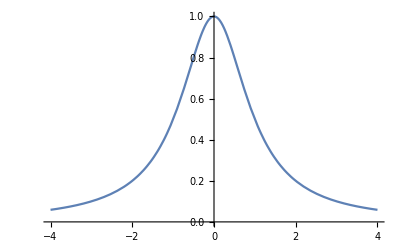

```mathematica
(* Problem #7 *)

f[x_]:=1/(1+x^2);
Plot[f[x],{x,-4,4}]
```

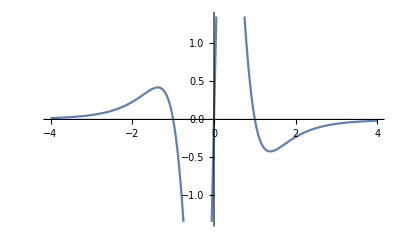

```mathematica
(* a. *)
fprime3[x_]=D[f[x],x,x,x];
Plot[fprime3[x],{x,-4,4}]
Solve[D[fprime3[x],x]==0,x];
```

```mathematica
zerosfprime4={};
For[i=1,i≤4,++i,
AppendTo[zerosfprime4,x/.Solve[D[fprime3[x],x]==0,x][[i]]]
];
(* N[Max[Abs[fprime3[zerosfprime4]]],6] *)
```

```mathematica
For[i=1,i≤4,++i,
Print["The third derivative of f evaluated at ",zerosfprime4[[i]]" is approximately equal to ",N[fprime3[zerosfprime4[[i]]],6]]
];
```

The third derivative of f evaluated at -√(1/5 (5-2 √5))  is approximately equal to -4.66856

The third derivative of f evaluated at √(1/5 (5-2 √5))  is approximately equal to 4.66856

The third derivative of f evaluated at -√(1/5 (5+2 √5))  is approximately equal to 0.420964

The third derivative of f evaluated at √(1/5 (5+2 √5))  is approximately equal to -0.420964

```mathematica
M=N[fprime3[zerosfprime4[[2]]],6];
Print["The maximal value of the third derivative of f on the interval {-4,4} is ",M];
```

The maximal value of the third derivative of f on the interval {-4,4} is 4.66856

```mathematica
(* b. *)
a=-4.2;
aVec={};
For[i=1,i≤41,++i,
a=a+.2;
If[Abs[a]<10^-5,
AppendTo[aVec,0],
AppendTo[aVec,a]
];
];
aVec
```

{-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.}

```mathematica
(* c. *)
poly={};
For[i=1,i≤40,++i,
A={};
xval={aVec[[i]],(aVec[[i]]+aVec[[i+1]])/2,x3=aVec[[i+1]]};
For[j=1,j≤3,++j,
row={};
For[k=1,k≤3,++k,
If[k==1,
AppendTo[row,1],
AppendTo[row,xval[[j]]^(k-1)]
];
];
AppendTo[A,row];
];
b={f[xval[[1]]],f[xval[[2]]],f[xval[[3]]]};
coef=LinearSolve[A,b];
t[x_]:={1,x,x^2}.coef;
AppendTo[poly,t[x]];
];
MatrixForm[poly]
```

(0.337092+0.111515 x+0.010487 x^2
0.368307+0.127956 x+0.0126519 x^2
0.403654+0.14761 x+0.0153838 x^2
0.443782+0.171236 x+0.0188614 x^2
0.489428+0.199793 x+0.0233279 x^2
0.541407+0.234484 x+0.029116 x^2
0.600576+0.276799 x+0.0366814 x^2
0.667751+0.328541 x+0.0466452 x^2
0.743543+0.391794 x+0.0598423 x^2
0.828035+0.468729 x+0.0773555 x^2
0.920214+0.561065 x+0.100479 x^2
1.01701+0.668799 x+0.130456 x^2
1.11185+0.78751 x+0.167605 x^2
1.1929+0.903323 x+0.208974 x^2
1.24234+0.985276 x+0.242935 x^2
1.24013+0.979315 x+0.239186 x^2
1.17835+0.821474 x+0.138417 x^2
1.08398+0.502028 x-0.131846 x^2
1.01599+0.159699 x-0.562748 x^2
1.+0.00571211 x-0.932978 x^2
1.-0.00571211 x-0.932978 x^2
1.01599-0.159699 x-0.562748 x^2
1.08398-0.502028 x-0.131846 x^2
1.17835-0.821474 x+0.138417 x^2
1.24013-0.979315 x+0.239186 x^2
1.24234-0.985276 x+0.242935 x^2
1.1929-0.903323 x+0.208974 x^2
1.11185-0.78751 x+0.167605 x^2
1.01701-0.668799 x+0.130456 x^2
0.920214-0.561065 x+0.100479 x^2
0.828035-0.468729 x+0.0773555 x^2
0.743543-0.391794 x+0.0598423 x^2
0.667751-0.328541 x+0.0466452 x^2
0.600576-0.276799 x+0.0366814 x^2
0.541407-0.234484 x+0.029116 x^2
0.489428-0.199793 x+0.0233279 x^2
0.443782-0.171236 x+0.0188614 x^2
0.403654-0.14761 x+0.0153838 x^2
0.368307-0.127956 x+0.0126519 x^2
0.337092-0.111515 x+0.010487 x^2)

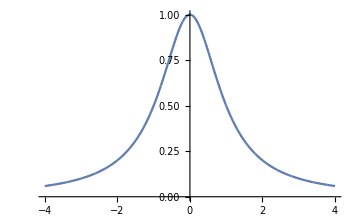

```mathematica
(* d. *)
plotf=Plot[f[x],{x,-4,4},PlotStyle->{Red,Dashed,Thick}];
plots={plotf};
For[i=1,i≤40,++i,
g[x_]=poly[[i]];
plot=Plot[g[x],{x,aVec[[i]],aVec[[i+1]]}];
AppendTo[plots,plot]
];
Show[plots]
(* plot of f with polynomials superimposed *)
```

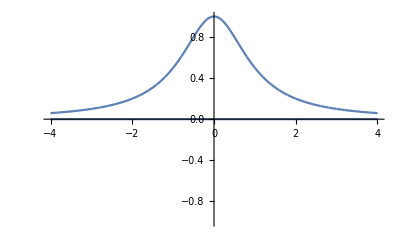

```mathematica
plots2={Plot[0,{x,-4,4}]};
For[i=1,i≤40,++i,
g[x_]=poly[[i]];
plot2=Plot[g[x],{x,aVec[[i]],aVec[[i+1]]}];
AppendTo[plots2,plot2]
];
Show[plots2]
(* plot of the polynomials only, along with the 0 function to get correct display *)
```

```mathematica
(* e. *)
```

```mathematica
(* f *)
(*from part e, it appears that the absolute error for the piecewise polynomial interpolation we have constructed is (M/6)*(0.2)^(number of subintervals), where M is as calculated in part a.  Since 0.2 < 1, as the number of subintervals -> infinity, (.2)^(number of subintervals)-> 0, and hence the absolute error -> 0.  *)
```